```mathematica
ClearAll["Global`*"]
```

```mathematica
g[y_]:={{1,0},{0,1+(z'[y])^2}}
```

```mathematica
detg[y_]:=Det[g[y]]
```

```mathematica
sqrtdetg[y_]:=Sqrt[detg[y]]
```

```mathematica
H[y_]:=1/2/( detg[y])^(3/2)z''[y]
```

```mathematica
σ[y_]:=σ0
```

```mathematica
(*solve for n^i omega_i == ψTOP at \partial \Omega_TOP*)
```

```mathematica
solTOP=Flatten[Solve[1/sqrtdetg[y] z'[y]==ψTOP,z'[y]]][[2]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

z'[y]→ψTOP/(√(1-ψTOP^2))

```mathematica
solBOTTOM=Flatten[Solve[-1/sqrtdetg[y] z'[y]==ψBOTTOM,z'[y]]][[2]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

z'[y]→ψBOTTOM/(√(1-ψBOTTOM^2))

```mathematica
L=1;
h=1;
κ=1;
σ0=1;
CC=1/10;
ϕTOP=CC;
ϕBOTTOM=0;
ψTOP=-CC;
ψBOTTOM=0;
```

```mathematica
eq={κ(-(1/sqrtdetg[y])D[H'[y]/sqrtdetg[y],y]-2( H[y])^3)+ σ [y]H[y]==0}//FullSimplify
```

{((5-30 z'[y]^2) z''[y]^3+2 (1+z'[y]^2) z''[y] ((1+z'[y]^2)^2+10 z'[y] z^(3)[y])-2 (1+z'[y]^2)^2 z^(4)[y])/(√(1+z'[y]^2))==0}

```mathematica
bcs={z[0]==ϕBOTTOM,z[h]==ϕTOP,z'[0]==(z'[y]/.solBOTTOM),z'[h]==(z'[y]/.solTOP)}
```

{z[0]==0,z[1]==1/10,z'[0]==0,z'[1]==-1/(3 √11)}

```mathematica
sys=Flatten[{eq,bcs}]
```

{((5-30 z'[y]^2) z''[y]^3+2 (1+z'[y]^2) z''[y] ((1+z'[y]^2)^2+10 z'[y] z^(3)[y])-2 (1+z'[y]^2)^2 z^(4)[y])/(√(1+z'[y]^2))==0,z[0]==0,z[1]==1/10,z'[0]==0,z'[1]==-1/(3 √11)}

```mathematica
sol=NDSolve[sys,z,{y,0,h},WorkingPrecision->30]
```

{{z→InterpolatingFunction[…]}}

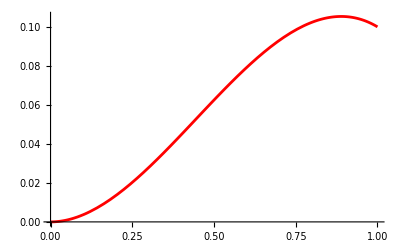

```mathematica
plotzexact=Plot[Evaluate[z[y]/.sol],{y,0,h},PlotRange->All,PlotStyle->Red]
```

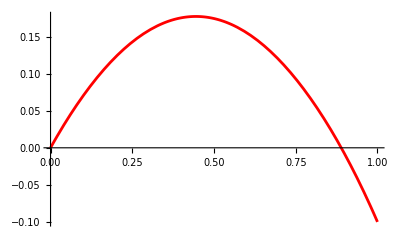

```mathematica
plotωexact=Plot[Evaluate[z'[y]/.sol],{y,0,h},PlotRange->All,PlotStyle->Red]
```

```mathematica
δ=1/100;
```

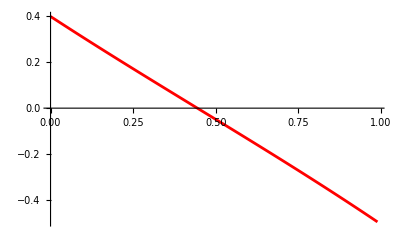

```mathematica
plotμexact=Plot[Evaluate[H[y]/.sol],{y,0,h-δ},PlotRange->All,PlotStyle->Red]
```

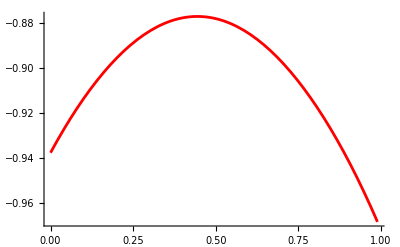

```mathematica
plotνexact=Plot[Evaluate[H'[y]/.sol],{y,0,h-δ},PlotRange->All,PlotStyle->Red]
```

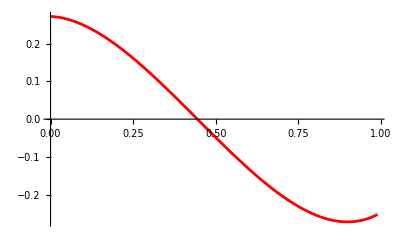

```mathematica
plotτexact=Plot[Evaluate[(1/sqrtdetg[y])D[H'[y]/sqrtdetg[y],y]/.sol],{y,0,h-δ},PlotRange->All,PlotStyle->Red]
```

```mathematica
epsilon = 1/20
```

1/20

```mathematica
(*check for z*)
```

```mathematica
t=Import["~/Documents/finite_elements/steady-state-no-flow/solution/z.csv"];
znum=Table[{t[[i,3]],t[[i,1]]},{i,2,Length[t]}]
```

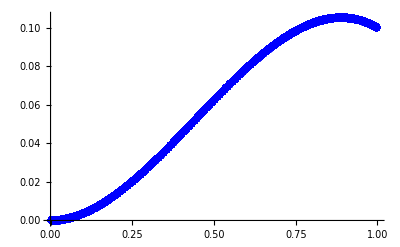

```mathematica
plotznum=ListPlot[znum,PlotStyle->{Blue,PointSize->0.01}]
```

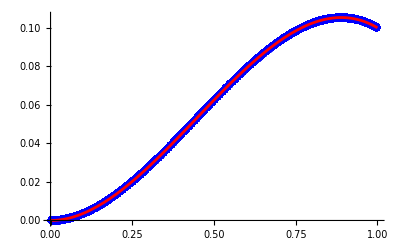

```mathematica
Show[plotznum,plotzexact]
```

```mathematica
(*check for ω*)
```

```mathematica
t=Import["~/Documents/finite_elements/steady-state-no-flow/solution/omega.csv"];
ωnum=Table[{t[[i,5]],t[[i,2]]},{i,2,Length[t]}]
```

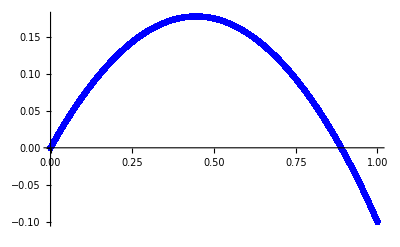

```mathematica
plotωnum=ListPlot[ωnum,PlotStyle->{Blue,PointSize->0.01}]
```

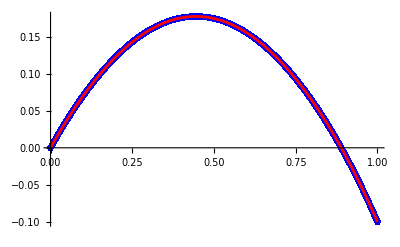

```mathematica
Show[plotωnum,plotωexact]
```

```mathematica
(*check for μ*)
```

```mathematica
t=Import["~/Documents/finite_elements/steady-state-no-flow/solution/mu.csv"];
μnum=Table[{t[[i,3]],t[[i,1]]},{i,1,Length[t]}]
```

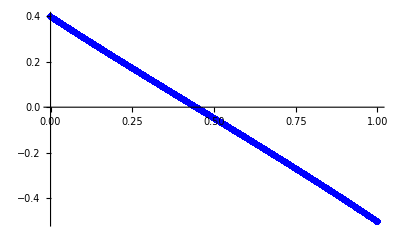

```mathematica
plotμnum=ListPlot[μnum,PlotStyle->{Blue,PointSize->0.01,Opacity->0.5}]
```

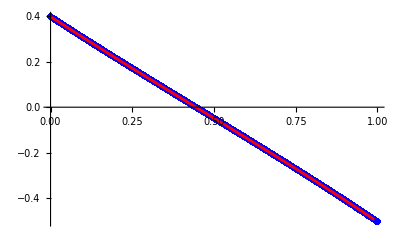

```mathematica
Show[plotμnum,plotμexact]
```

```mathematica
(*check for τ*)
```

```mathematica
t=Import["~/Documents/finite_elements/steady-state-no-flow/solution/tau.csv"];
τnum=Table[{t[[i,3]],t[[i,1]]},{i,1,Length[t]}]
```

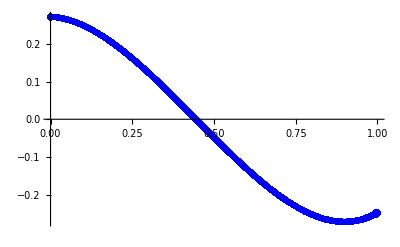

```mathematica
plotτnum=ListPlot[τnum,PlotStyle->{Blue,PointSize->0.01,Opacity->0.5}]
```

```mathematica
Show[plotτnum,plotτexact,PlotRange->{-1,1}]
```

-Graphics-